### a)

```mathematica
M = {{σ+1,3},{-2,σ-1}};
λ=Eigenvalues[M]
```

```mathematica
{-ⅈ √5+σ,ⅈ √5+σ}
```

### b)

```mathematica
x=.;y=.;
X[t_] = {x[t],y[t]};
Dynsystem = X'[t]==M.X[t];
sol = DSolve[Dynsystem,{x,y},t];
X[t_,x0_,y0_,σ_] = {x[t],y[t]} /. sol /. {C[1]->u,C[2]->v}
```

```mathematica
{{(3 ⅇ^(t σ) v Sin[√5 t])/(√5)+1/5 ⅇ^(t σ) u (5 Cos[√5 t]+√5 Sin[√5 t]),-(2 ⅇ^(t σ) u Sin[√5 t])/(√5)+1/5 ⅇ^(t σ) v (5 Cos[√5 t]-√5 Sin[√5 t])}}
```

### c)

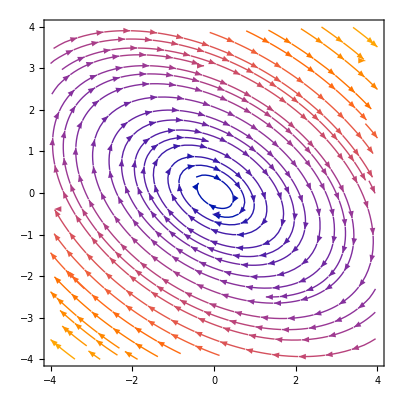

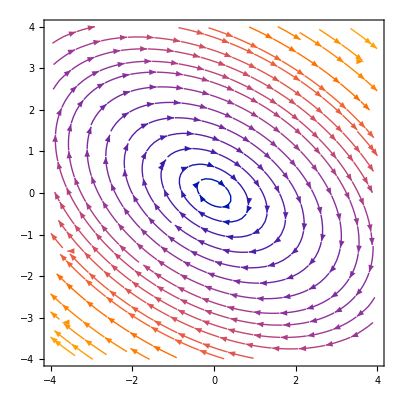

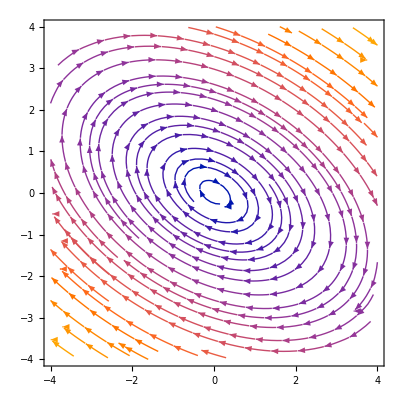

```mathematica
plot1 =StreamPlot[{(σ+ 1)x + 3y, -2x + (σ-1)y} /. {σ -> -1/10},{x,-4,4},{y,-4,4}];
plot2 = StreamPlot[{(σ+ 1)x + 3y, -2x + (σ-1)y} /. {σ -> 0},{x,-4,4},{y,-4,4}];
plot3 = StreamPlot[{(σ+ 1)x + 3y, -2x + (σ-1)y} /. {σ -> 1/10},{x,-4,4},{y,-4,4}];
Show[plot1]
Show[plot2]
Show[plot3]
```

### d)

```mathematica
Solve[X[0,u,v,0]==X[t,u,v,0],t]
```

```mathematica
{{t->ConditionalExpression[(2 π C[1])/(√5), C[1]∈Integers]}}
```

### e)

```mathematica
solution = {1/5 ⅇ^(t σ) (5 u Cos[√5 t]+√5 u Sin[√5 t]+3 √5 v Sin[√5 t]),-1/5 ⅇ^(t σ) (-5 v Cos[√5 t]+2 √5 u Sin[√5 t]+√5 v Sin[√5 t])};
major = FindMaximum[Norm[solution]/. {u->1,v->1,σ->0},t];
minor = FindMinimum[Norm[solution] /. {u->1,v->1,σ->0},t];
ratio = major/minor
```

```mathematica
{1.6180339887498942,{(t->0.6376910210893485)/(t->1.3401724846165075)}}
```

### f)

```mathematica
direction = solution /. {u->1,v->1,σ->0,major[[2]][[1]]};
Normalize[direction]
```

{0.850651-0.525731}